# Different Distribution Types

## Gamma Distributions

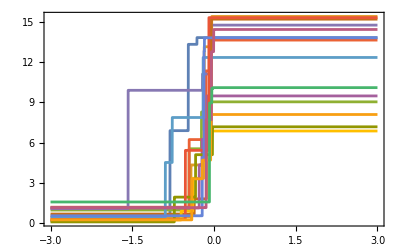
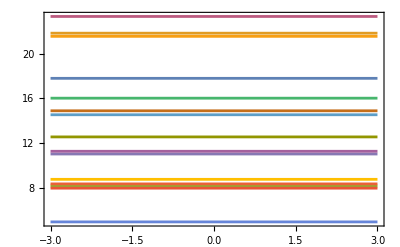
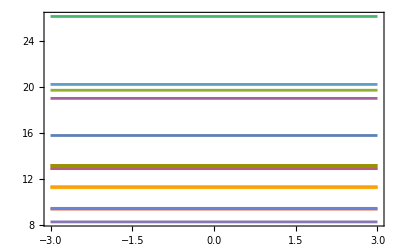
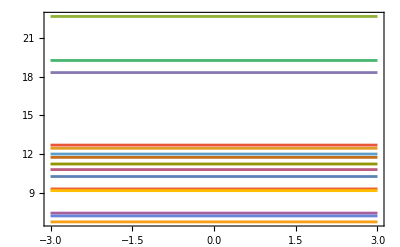
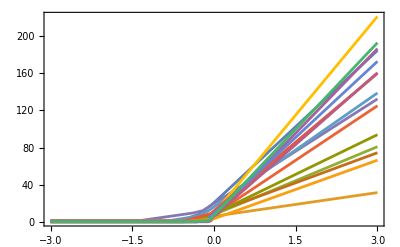
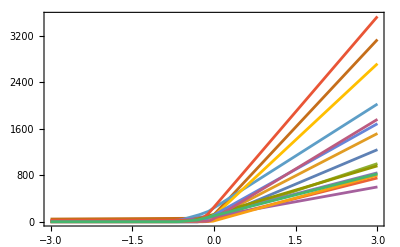
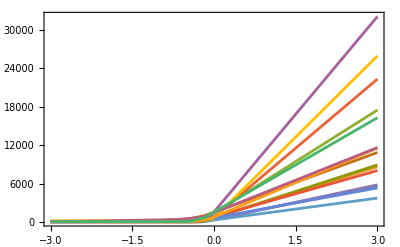
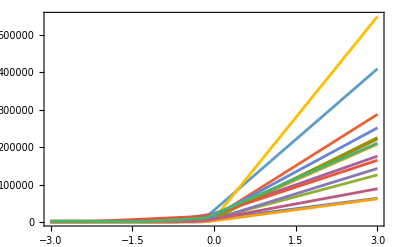
Threshold | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Ramp | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Tanh | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Sin | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LogisticSigmoid | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{netPlots=ResourceFunction[ResourceObject[<|"Name"->"NetGraphPlot","UUID"->"36d2c387-8948-4767-8860-5d698a62e3d1","ResourceType"->"Function","ResourceLocations"->{CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1"]},"Version"->None,"DocumentationLink"->URL["https://www.wolframcloud.com/obj/sw-writings0/ChatTechNetGraphPlot"],"ExampleNotebookData"->Automatic,"FunctionLocation"->CloudObject["https://www.wolframcloud.com/obj/sw-writings0/Resources/36d/36d2c387-8948-4767-8860-5d698a62e3d1/download/DefinitionData"],"ShortName"->"NetGraphPlot","SymbolName"->"FunctionRepository`$36d2c3878948476788605d698a62e3d1`NetGraphPlot"|>]][NetChain[Append[Catenate@Table[{3},#],{}],"Input"->"Real"],EdgeStyle->GrayLevel[.3,.5],EdgeShapeFunction->"Line",ImageSize->Tiny,AspectRatio->1/2]&/@Range[4]},SeedRandom[1234];
Grid[Append[Prepend[netPlots,""]]@Table[Prepend[Text[act/. Function[x,If[x>0,1,0]]->"Threshold"]]@Table[With[{netInit=NetChain[Append[Catenate@Table[{3,ElementwiseLayer[act]},depth],{}],"Input"->"Real"]},Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->GammaDistribution[2,2],"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[x];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None]],{depth,{1,2,3,4}}],{act,{Function[x,If[x>0,1,0]],Ramp,Tanh,Sin,LogisticSigmoid}}]]]
```